## Bifurcation diagram: Ricker model

```mathematica
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
SetDirectory["/Users/tbury/Google Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_std"];
```

```mathematica
(* Import bifurcation data points *)
bifDataRb= Import["bifurcation/data/r_vary.csv"]; (* varing r *)
```

```mathematica
(* Figure parameters *)
ps = 0.002;
```

### Varying rb

```mathematica
bifDataRb[[1]]
```

{,Time,Pop,r}

```mathematica
pData=bifDataRb[[2;;,{4,3}]];
```

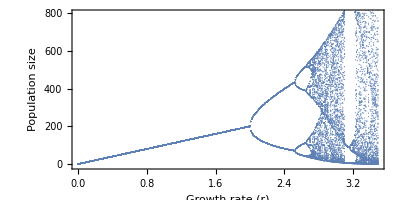

```mathematica
bifPlotRb=ListPlot[pData,
Frame->True,
FrameLabel->{{"Population size",None},{"Growth rate (r)",None}},
PlotRange->{-10,800},
PlotStyle->{Directive[{TMBcolours[[1]],PointSize[ps]}],
Directive[{TMBcolours[[2]],PointSize[ps]}]},
AspectRatio->0.5,
Axes->False,
ImageSize->400,
LabelStyle->12]
```

### Export figure

```mathematica
Export["figures/bif.png",bifPlotRb,ImageResolution->200];
```